Логаш Полина Вариант 7

Задание 1

{-4.01+20.106 X,True,4.24718}

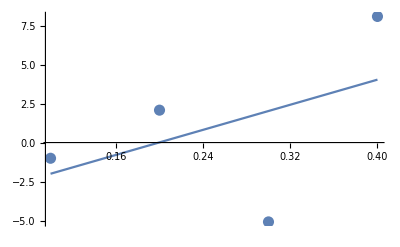

```mathematica
x = {0.1, 0.2, 0.3, 0.4};
y = {-1.007, 2.076, -5.085, 8.082};
n =Length[x]; Tbl=Table[{x[[i]], y[[i]]}, {i, 1, n}];
eqv:=Table[∑_(i=0)^m Subscript[α, i]*∑_(j=1)^n (x⟦j⟧)^(i+k)==∑_(j=1)^n (y⟦j⟧)*(x⟦j⟧)^k,{k,0,m}];
Koef:=Solve[eqv,Table[Subscript[α, i],{i,0,m}]]//Flatten;
P[X_]:=(∑_(i=0)^m Subscript[α, i]*X^i)/.Koef
Ft[X_]:=Fit[Tbl,Table[X^i,{i,0,m}],X]
δ:=√(1/n*∑_(i=1)^n (y⟦i⟧-P[x⟦i⟧])^2)//N
Gr:=Show[ListPlot[Tbl,PlotStyle-> {PointSize[0.02]}],Plot[P[X],{X,x[[1]],x[[n]]}]]
m=1;{P[X],((P[X]-Ft[X])//Chop)==0,δ}
Gr
```

{8.595-105.944 X+252.1 X^2,True,3.41805}

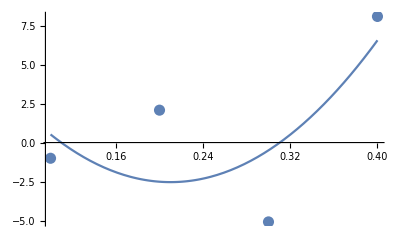

```mathematica
m=2;{P[X],((P[X]-Ft[X])//Chop)==0,δ}
Gr
```

Задание 2;

3

{-44.906+744.977 X-3569.4 X^2+5095.33 X^3,True,7.3535×10^-12,True}

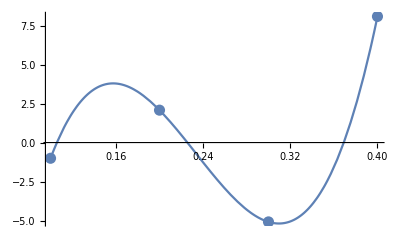

```mathematica
eps=1/2 10^-2;
m=1;While[δ>1/2 10^-2,m=m+1]
m1=m
{P[X],Chop[P[X]-Ft[X],10^-7]==0,δ1=δ,δ1<eps}
Gr
```

```mathematica
m=m-1;
m2=m
{P[X],((P[X]-Ft[X])//Chop)==0,δ2=δ,δ2<eps}
Gr
```

2

{8.595-105.944 X+252.1 X^2,True,3.41805,False}

-Graphics-

```mathematica
If[(k1=eps/δ1)<(k2=δ1/eps),opt=m1,opt=m2]
```

2